```mathematica
Needs["VariationalMethods`"]
```

```mathematica
Reduce[z≥1&&θ≥0&&z-θ≥0&&θ≤2&&(-θ/2+1)(-θ/2+z-1)≥0,{z,θ}]
```

(z==1&&θ==0)||(1<z≤2&&0≤θ≤-2+2 z)||(z>2&&0≤θ≤2)

```mathematica
Reduce[z≥1&&θ≥0&&z-θ≥0&&θ≤2&&(-θ/2+1)(-θ/2+z-1)≥0,{θ,z}]
```

0≤θ≤2&&z≥(2+θ)/2

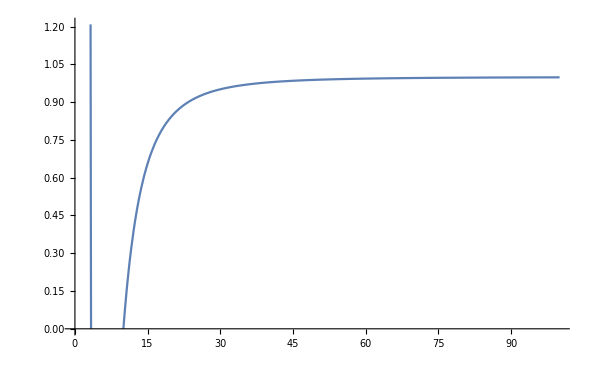

```mathematica
Plot[
1-(rh/r)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) rh^(2z-2θ)/r^(2(z-θ+1))(1-(rh/r)^(θ-z))/.{z->1.5,θ->0.5,μ-> 12,rh->10},{r,0,100},AxesOrigin->{0,0}
]
```

```mathematica
Solve[
(1-(rh/r)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) rh^(2z-2θ)/r^(2(z-θ+1))(1-(rh/r)^(θ-z))/.{z->1.5,θ->0.5,μ-> 12,rh->10})==0,r
]
```

{{r→-6.66296-9.99629 ⅈ},{r→-6.66296+9.99629 ⅈ},{r→3.32592},{r→10.}}

```mathematica
Block[
{f,r,rh,z,θ,μ,t,q},
f[r_,rh_,μ_,z_,θ_]:=1-(rh/r)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) rh^(2z-2θ)/r^(2(z-θ+1))(1-(rh/r)^(θ-z));
EulerEquations[-r[t]^(1-θ/2)Sqrt[r[t]^(2z-2)f[r[t],rh,μ,z,θ]-r'[t]^2/r[t]^4/f[r[t],rh,μ,z,θ]]+q μ(1-(rh/r[t])^(z-θ)),r[t],t]
]
```

(q (z-θ) μ (rh/r[t])^(z-θ))/r[t]-((-3-θ/2) r[t]^(-4-θ/2) r'[t]^2)/((1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))) √(r[t]^(-2+2 z) (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))-r'[t]^2/(r[t]^4 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))))))+(r[t]^(-6-θ/2) (2 rh^2 (-2+θ) (-2-z+θ) (rh/r[t])^(z-θ)-2 rh^(2 (z-θ)) (z-θ) (1+z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 z+2 θ)-rh^(2 (z-θ)) (z-θ)^2 μ^2 (rh/r[t])^(-z+θ) r[t]^(-2 z+2 θ)) r'[t]^2)/(2 (2-θ) (-1+(rh/r[t])^(2+z-θ)-(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))^2 √(r[t]^(-2+2 z) (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))-r'[t]^2/(r[t]^4 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))))))+1/2 (-2+θ) r[t]^(-θ/2) √(r[t]^(-2+2 z) (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))-r'[t]^2/(r[t]^4 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))))+(r[t]^(1-θ/2) (-2 (-1+z) r[t]^(-3+2 z) (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))+1/(2 (2-θ))r[t]^(-5+2 z) (-2 rh^2 (-2+θ) (-2-z+θ) (rh/r[t])^(z-θ)+2 rh^(2 (z-θ)) (z-θ) (1+z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 z+2 θ)+rh^(2 (z-θ)) (z-θ)^2 μ^2 (rh/r[t])^(-z+θ) r[t]^(-2 z+2 θ))-(4 r'[t]^2)/(r[t]^5 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))))+((-2 rh^2 (-2+θ) (-2-z+θ) (rh/r[t])^(z-θ)+2 rh^(2 (z-θ)) (z-θ) (1+z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 z+2 θ)+rh^(2 (z-θ)) (z-θ)^2 μ^2 (rh/r[t])^(-z+θ) r[t]^(-2 z+2 θ)) r'[t]^2)/(2 (2-θ) r[t]^7 (-1+(rh/r[t])^(2+z-θ)-(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))^2)))/(2 √(r[t]^(-2+2 z) (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))-r'[t]^2/(r[t]^4 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))))))-(r[t]^(-3-θ/2) r''[t])/((1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))) √(r[t]^(-2+2 z) (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))-r'[t]^2/(r[t]^4 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))))))+(r[t]^(-3-θ/2) r'[t] (2 (-1+z) r[t]^(-3+2 z) (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))) r'[t]+1/(2 (2-θ))r[t]^(-5+2 z) (2 rh^2 (-2+θ) (-2-z+θ) (rh/r[t])^(z-θ)-2 rh^(2 (z-θ)) (z-θ) (1+z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 z+2 θ)-rh^(2 (z-θ)) (z-θ)^2 μ^2 (rh/r[t])^(-z+θ) r[t]^(-2 z+2 θ)) r'[t]+(4 r'[t]^3)/(r[t]^5 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))))+((2 rh^2 (-2+θ) (-2-z+θ) (rh/r[t])^(z-θ)-2 rh^(2 (z-θ)) (z-θ) (1+z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 z+2 θ)-rh^(2 (z-θ)) (z-θ)^2 μ^2 (rh/r[t])^(-z+θ) r[t]^(-2 z+2 θ)) r'[t]^3)/(2 (2-θ) r[t]^7 (-1+(rh/r[t])^(2+z-θ)-(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))^2)-(2 r'[t] r''[t])/(r[t]^4 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))))))/(2 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))) (r[t]^(-2+2 z) (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))-r'[t]^2/(r[t]^4 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))))^(3/2))==0

```mathematica
Block[
{qcrit,rz1,fr1,μextreme},
qcrit[rs_,rh_,μ_,z_,θ_]:=Sqrt[1-(rh/rs)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) rh^(2z-2θ)/rs^(2(z-θ+1))(1-(rh/rs)^(θ-z))]/(μ rs(1-(rh/rs)^(z-θ)));
μextreme[rs_,rh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]rh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
rz1[q_,rs_,rh_,μ_,z_,θ_]:=NDSolveValue[
{(q (z-θ) μ (rh/r[t])^(z-θ))/r[t]-((-3-θ/2) r[t]^(-4-θ/2) r'[t]^2)/((1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))) √(r[t]^(-2+2 z) (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))-r'[t]^2/(r[t]^4 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))))))+(r[t]^(-6-θ/2) (2 rh^2 (-2+θ) (-2-z+θ) (rh/r[t])^(z-θ)-2 rh^(2 (z-θ)) (z-θ) (1+z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 z+2 θ)-rh^(2 (z-θ)) (z-θ)^2 μ^2 (rh/r[t])^(-z+θ) r[t]^(-2 z+2 θ)) r'[t]^2)/(2 (2-θ) (-1+(rh/r[t])^(2+z-θ)-(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))^2 √(r[t]^(-2+2 z) (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))-r'[t]^2/(r[t]^4 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))))))+1/2 (-2+θ) r[t]^(-θ/2) √(r[t]^(-2+2 z) (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))-r'[t]^2/(r[t]^4 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))))+(r[t]^(1-θ/2) (-2 (-1+z) r[t]^(-3+2 z) (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))+1/(2 (2-θ))r[t]^(-5+2 z) (-2 rh^2 (-2+θ) (-2-z+θ) (rh/r[t])^(z-θ)+2 rh^(2 (z-θ)) (z-θ) (1+z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 z+2 θ)+rh^(2 (z-θ)) (z-θ)^2 μ^2 (rh/r[t])^(-z+θ) r[t]^(-2 z+2 θ))-(4 r'[t]^2)/(r[t]^5 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))))+((-2 rh^2 (-2+θ) (-2-z+θ) (rh/r[t])^(z-θ)+2 rh^(2 (z-θ)) (z-θ) (1+z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 z+2 θ)+rh^(2 (z-θ)) (z-θ)^2 μ^2 (rh/r[t])^(-z+θ) r[t]^(-2 z+2 θ)) r'[t]^2)/(2 (2-θ) r[t]^7 (-1+(rh/r[t])^(2+z-θ)-(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))^2)))/(2 √(r[t]^(-2+2 z) (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))-r'[t]^2/(r[t]^4 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))))))-(r[t]^(-3-θ/2) r''[t])/((1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))) √(r[t]^(-2+2 z) (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))-r'[t]^2/(r[t]^4 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))))))+(r[t]^(-3-θ/2) r'[t] (2 (-1+z) r[t]^(-3+2 z) (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))) r'[t]+1/(2 (2-θ))r[t]^(-5+2 z) (2 rh^2 (-2+θ) (-2-z+θ) (rh/r[t])^(z-θ)-2 rh^(2 (z-θ)) (z-θ) (1+z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 z+2 θ)-rh^(2 (z-θ)) (z-θ)^2 μ^2 (rh/r[t])^(-z+θ) r[t]^(-2 z+2 θ)) r'[t]+(4 r'[t]^3)/(r[t]^5 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))))+((2 rh^2 (-2+θ) (-2-z+θ) (rh/r[t])^(z-θ)-2 rh^(2 (z-θ)) (z-θ) (1+z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 z+2 θ)-rh^(2 (z-θ)) (z-θ)^2 μ^2 (rh/r[t])^(-z+θ) r[t]^(-2 z+2 θ)) r'[t]^3)/(2 (2-θ) r[t]^7 (-1+(rh/r[t])^(2+z-θ)-(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))^2)-(2 r'[t] r''[t])/(r[t]^4 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))))))/(2 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ))) (r[t]^(-2+2 z) (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))-r'[t]^2/(r[t]^4 (1-(rh/r[t])^(2+z-θ)+(rh^(2 (z-θ)) (z-θ) μ^2 (1-(rh/r[t])^(-z+θ)) r[t]^(-2 (1+z-θ)))/(2 (2-θ)))))^(3/2))==0,r[0]== rs,r'[0]==0},r,{t,0.1,5.7}
];
fr1[t_,q_,rs_,rh_,μ_,z_,θ_]:=rz1[q,rs,rh,μ,z,θ][t];
Print[μextreme[1,10,1.5,0.5]," ", qcrit[1,10,0.75μextreme[1,10,1.5,0.5],1.5,0.5]]
(*Show[
ListLinePlot[Table[{i,Abs[fr1[i,0,0.1,1,0.75μextreme[0.1,1,1.5,0.5],1.5,0.5]]},{i,0.1,5,0.05}]],
ListLinePlot[Table[{i,Abs[fr1[i,0.75 qcrit[0.1,1,0.75μextreme[0.1,1,1.5,0.5],1.5,0.5]//Abs,0.1,1,0.75μextreme[0.1,1,1.5,0.5],1.5,0.5]]},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[fr1[i,qcrit[0.1,1,0.75μextreme[0.1,1,1.5,0.5],1.5,0.5]//Abs,0.1,1,0.75μextreme[0.1,1,1.5,0.5],1.5,0.5]]},{i,0.1,5,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[fr1[i,5qcrit[0.1,1,0.75μextreme[0.1,1,1.5,0.5],1.5,0.5]//Abs,0.1,1,0.75μextreme[0.1,1,1.5,0.5],1.5,0.5]]},{i,0.1,5,0.05}],PlotStyle->Green],
PlotRange->{{0.1,5},{0.39,0.4}},AxesOrigin->{0,0.39}
]*)
]
```

18.1959 -0.551495